```mathematica
data=Import["C:\\Users\\HILL\\Downloads\\multiple.csv"];
```

```mathematica
fontsize=44;
```

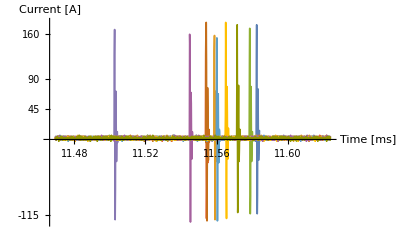

```mathematica
ListLinePlot[
Table[
Thread[{data⟦All,1⟧,data⟦All,j⟧}],{j,2,11}],
PlotRange->All,
PlotStyle->{Thickness[0.003]},
TicksStyle->{Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"],Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"]},
AxesStyle->{{Thick,Black},{Thick,Black}},AxesLabel->{Style["Time [ms]",Black,FontFamily->"Helvetica",FontSize->fontsize],Style["Current [A]",Black,FontFamily->"Helvetica",FontSize->fontsize]},
Ticks->
{{{0.01148,11.48,0.06,Directive[Thick]},
{0.01152,11.52,0.06,Directive[Thick]},
{0.01156,11.56,0.06,Directive[Thick]},
{0.01160,"11.60",0.06,Directive[Thick]}}
,{{2,45,0.04},{4,90,0.04},{7,160,0.04},{-5,-115,0.04}}
},
ImageSize->Full]
```